# Visualizing Atomic Orbitals

Jingbo Wang, Paul C. Abbott, and Jim F. Williams

The School of Physics, M013
The University of Western Australia
35 Stirling Highway
Crawley WA 6009
Australia

paul.c.abbott@uwa.edu.au

The Mathematica software package provides a range of tools for working with atomic systems. The symbolic tools include orthogonal polynomials and Clebsch-Gordan coefficients whilst the graphical capabilities cover polar plots; spherical plots; density plots; contour plots in two and three dimensions; and animation. These tools are applied to the manipulation and visualization of atomic orbitals.

## INTRODUCTION

The probability distribution of the electron charge cloud in an atom, namely the atomic orbital, often reveals crucial information in atomic physics. Visual representation of such orbitals is invaluable to researchers working in this field and also helps teaching atomic structures to physics or chemistry students.  The atomic orbital concepts were discussed in detail by Berry and the cited papers therein, including several visualization devices. However, the newly developed symbolic package Mathematica provides a wider range of graphical tools (including polar plots, spherical plots, density plots, contour plots in two and three dimensions, and animation), which can be applied to help visualise the radial and angular behaviour of multi-dimensional systems.

Mathematica also has a wide range of built-in special functions appropriate for the analysis of quantum systems. Orthogonal polynomials — Legendre, Laguerre, Chebyshev, Hermite and Jacobi (corresponding to the Mathematica functions P_n(x), L_n^a(x), U_n(x), T_n(x), H_n(x), and P_n^(a,b)(x)) — arise when solving a wide class of eigenvalue and boundary value problems. The spherical harmonics, Y_l^m(θ,ϕ), are eigenfunctions of the angular part of the Laplacian operator (which is the quantum mechanical angular momentum operator). Clebsch-Gordan coefficients arise in the study of angular momenta in quantum mechanics, and in other applications of the rotation group.  These functions, taken together with the orthogonal polynomials and graphical tools, provide a powerful environment for the study of atomic systems. It is worth noting that these methods can be readily utilized in the studies of  other multi-dimensional systems.

As this article is not intended to be a tutorial on Mathematica, commands and syntax will not usually be explained. However, it is hoped that by showing a well-chosen set of examples, even readers unfamiliar with Mathematica will be able to follow the examples.  The graphical output is placed immediately after its corresponding input command as it appears in Mathematica notebooks. Arbitrary units are used in these graphs.

## Section. NOTATION AND PREREQUISITES

The quantity

Ω(r)ⅆr={|ψ_(n,l,m)(r)| ⅆr | pure basis state | ψ_(n,l,m)(r),
|ψ_(n,l)(r)|ⅆr | coherently mixed state | ψ_(n,l)(r)=∑_m c_m ψ_(n,l,m)(r),

where

ψ_(n,l,m)(r)≡|n l m⟩=R_(n,l)(r)Y_l^m(θ,ϕ), r=(r,θ,ϕ),ⅆr=r^2 ⅆrⅆΩ, ⅆΩ=sin(θ)ⅆθⅆϕ,

represents the probability of finding an electron in the volume element ⅆr. The spherical harmonics, Y_l^m(θ,ϕ), give the angular distribution of the atomic orbitals and R_(n,l)(r) is the corresponding radial distribution.

In the following, the general spherical harmonic will be denoted using the Mathematica shorthand Y_l^m(θ,ϕ). For example,

```mathematica
Subscript[Y, 2]^1(θ,ϕ)
```

-1/2 √(15/(2 π)) ⅇ^(ⅈ ϕ) sin(θ) cos(θ)

Complex conjugation, required to yield real-valued charge densities, is easily achieved using a replacement rule:

```mathematica
SuperStar[exp_]:=exp/.Complex[a_,b_]->Complex[a,-b]
```

For example,

```mathematica
SuperStar[Subscript[Y, 2]^1(θ,ϕ)]
```

-1/2 √(15/(2 π)) ⅇ^(-ⅈ ϕ) sin(θ) cos(θ)

We make use of the Notation package to define custom input and output notations.

```mathematica
<<Notation`
```

```mathematica
Symbolize[j']
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

## Section. ANGULAR DISTRIBUTION OF ATOMIC ORBITALS

### Subsection. Pure states ψ_(n,l,m)(r)

For pure basis states, ψ_(n,l,m)(r), the angular distribution:

Ω_(l,m)^ang(θ)=Abs[Y_l^m(θ,ϕ)]^2,

is axially symmetric with respect to the azimuthal angle ϕ. In this case, PolarPlot can provide a complete view of the atomic orbitals.

After defining the angular distribution function:

```mathematica
Subscript[Ω, l_,m_](θ_):=Subscript[Y, l]^m(θ,ϕ) SuperStar[Subscript[Y, l]^m(θ,ϕ)]
```

individual charge densities can be immediately examined, e.g.,

```mathematica
Subscript[Ω, 3,2](θ)
```

(105 sin^4(θ) cos^2(θ))/(32 π)

Here are plots of the atomic orbitals for the states l=1,2,3, m=0,…,l.

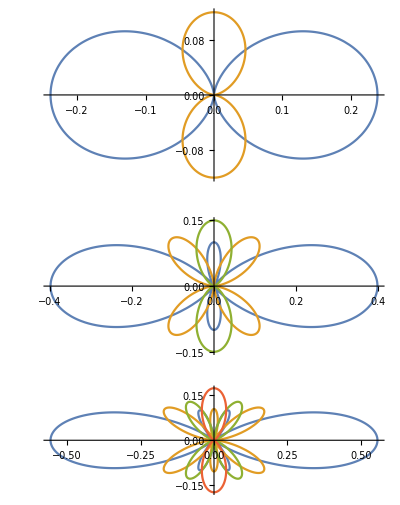

```mathematica
GraphicsColumn@Table[PolarPlot[Evaluate[Table[Subscript[Ω, l,m](θ),{m,0,l}]],{θ,0,2 π},PlotRange->All],{l,1,3}]
```

```mathematica
Manipulate[PolarPlot[Evaluate[Subscript[Ω, l,m](θ)],{θ,0,2 π},AspectRatio->Automatic,PlotRange->{{-0.8,0.8},{-0.3,0.3}}],{l,Range[4]},{{m,0},Range[0,l],ControlType->SetterBar}]
```

### Subsection. Mixed states ∑_m c_m ψ_(n,l,m)(r)

For coherently mixed states

ψ_(n,l)(r)=∑_m c_m ψ_(n,l,m)(r)=r R_(n,l)(r)∑_m c_m Y_l^m(θ,ϕ),

the angular probability distribution is

Ω_l^ang(θ,ϕ)=(|∑_m c_m Y_l^m(θ,ϕ)|)^2.

In this case, the charge cloud is no longer axially symmetric and its distribution is a function of both θ and ϕ. Three-dimensional plots are thus required to depict the structure of the coherently mixed atomic orbitals.

In general, the expression

ω_l(θ,ϕ)=∑_(m=-l,2)^l a_m ⅇ^(ⅈ b_m)Y_l^m(θ,ϕ),

where a_m (b_m) are the amplitude ratio (relative phase) of each state, can be evaluated in Mathematica using:

```mathematica
Subscript[ω, l_][c_][θ_,ϕ_]:=Subscript[ω, l][c][θ,ϕ]=∑_(i=0)^l c_⟦i+1,1⟧ ⅇ^(ⅈ c_⟦i+1,2⟧) Subscript[Y, l]^(l-2i)(θ,ϕ)
```

The argument to c needs to be a list of {a_m,b_m} pairs. The general angular charge distribution then reads:

```mathematica
Subscript[Ω, l_][c_][θ_,ϕ_]:=Factor[ComplexExpand[Expand[Subscript[ω, l](c)(θ,ϕ) SuperStar[Subscript[ω, l](c)(θ,ϕ)]]]]
```

where the core of this expression is the product of ω_l(c)(θ,ϕ) with its complex conjugate, ω_l(c)(θ,ϕ)^*. The other operations, Expand, ComplexExpand, and Factor, are used to simplify the expression to a human readable form.

As an example, for the general P-state wavefunction can be obtained from the mixed state consisting of l=1, m=±1:

```mathematica
Subscript[ψ, P](a_,b_)=Subscript[Ω, 1][({{1, 0}, {a, b}})][θ,ϕ]
```

(3 sin^2(θ) (a^2-2 a cos(b-2 ϕ)+1))/(8 π)

and then plot the orbitals for the states with parameters {a=0.1,b=0}:

```mathematica
Manipulate[SphericalPlot3D[Evaluate[Subscript[ψ, P](a,b)],{θ,0,π},{ϕ,0,2 π},BoxRatios->1,PlotRange->0.5],{{a,0.1},0,1},{b,0,π}]
```

Note that the full range of ϕ was not shown to highlight the structure of the orbital.

For a more complicated atomic orbitals, such as a coherently excited F-state atom, the charge density reads

```mathematica
Subscript[ψ, F][θ_,ϕ_]:=Subscript[Ω, 3][({{Subscript[a, 3], Subscript[b, 3]}, {Subscript[a, 1], 0}, {Subscript[a, -1], Subscript[b, -1]}, {Subscript[a, -3], Subscript[b, -3]}})][θ,ϕ];Subscript[ψ, F][θ,ϕ]
```

1/(64 π)7 sin^2(θ) (-150 a_-1 a_1 cos^4(θ) cos(2 ϕ-b_-1)+60 a_-1 a_1 cos^2(θ) cos(2 ϕ-b_-1)+10 √15 a_-3 a_-1 sin^2(θ) cos^2(θ) cos(-b_-3+b_-1+2 ϕ)-10 √15 a_-3 a_1 sin^2(θ) cos^2(θ) cos(4 ϕ-b_-3)-10 √15 a_-1 a_3 sin^2(θ) cos^2(θ) cos(-b_-1+b_3+4 ϕ)+10 √15 a_1 a_3 sin^2(θ) cos^2(θ) cos(b_3+2 ϕ)-10 a_-3 a_3 sin^4(θ) cos(-b_-3+b_3+6 ϕ)-2 √15 a_-3 a_-1 sin^2(θ) cos(-b_-3+b_-1+2 ϕ)+2 √15 a_-3 a_1 sin^2(θ) cos(4 ϕ-b_-3)+2 √15 a_-1 a_3 sin^2(θ) cos(-b_-1+b_3+4 ϕ)-2 √15 a_1 a_3 sin^2(θ) cos(b_3+2 ϕ)-6 a_-1 a_1 cos(2 ϕ-b_-1)+5 a_-3^2 sin^4(θ)+5 a_3^2 sin^4(θ)+75 a_-1^2 cos^4(θ)+75 a_1^2 cos^4(θ)-30 a_-1^2 cos^2(θ)-30 a_1^2 cos^2(θ)+3 a_-1^2+3 a_1^2)

Choosing the parameters arbitrarily as

```mathematica
a/:Subscript[a, 1]=1.0;a/:Subscript[a, -1]=0.0;a/:Subscript[a, 3]=0.8;a/:Subscript[a, -3]=0.05;
```

```mathematica
b/:Subscript[b, -1]=π;b/:Subscript[b, 3]=π/5;b/:Subscript[b, -3]=π/4;
```

one can produce a three-dimensional graph:

```mathematica
SphericalPlot3D[Evaluate[Subscript[ψ, F](θ,ϕ)],{θ,0,π},{ϕ,0,2 π},PlotRange->All]
```

-Graphics3D-

Here we plot the previously defined F-state orbital with a new set of parameters.

```mathematica
a/:Subscript[a, 1]=0.3;a/:Subscript[a, -1]=1.0;a/:Subscript[a, 3]=0.8;a/:Subscript[a, -3]=0.2;
```

```mathematica
b/:Subscript[b, -1]=π;b/:Subscript[b, 3]=π/5;b/:Subscript[b, -3]=π/4;
```

```mathematica
SphericalPlot3D[Evaluate[Subscript[ψ, F](θ,ϕ)],{θ,0,π},{ϕ,0,2 π},PlotRange->All]
```

-Graphics3D-

We clear the values assigned in this section.

```mathematica
Clear[a,b];
```

### Subsection. Time evolution of atomic orbitals

Due to the interaction between the intrinsic magnetic dipole moment of the electron (spin) and the internal magnetic field of the atom (orbital angular momentum), the atomic charge density evolves with time. Animation provides views of such dynamic effects. Taking the spin-orbit (L-S) coupling into account, we obtained the time-dependent charge density function for a mixed state:

ψ_(n,l)(r)=∑_m c_m ψ_(n,l,m)(r),

Ω_(n,l)^ang(θ,ϕ,t)=∑_(K,Q,m,m') (-1)^(l-m')√(2K+1)( l | l | K
m | -m | -Q )Y_l^m'(θ,ϕ)(Y_l^m(θ,ϕ))^*⟨(T(l))_(K,Q)^†⟩G_K(l,s;t),

where

⟨(T(l))_(K,Q)^†⟩=∑_(m,m') (-1)^(l-m')√(2K+1)( l | l | K
m' | -m | -Q )c_m' c_m^*

implemented in Mathematica as

```mathematica
Subscript[𝒯, K_,Q_][l_]:=Subscript[𝒯, K,Q](l)=∑_(m=-l)^l (-1)^(l-(m+Q)) √(2 K+1)( {{l, l, K}, {m+Q, -m, -Q}} )Subscript[c, m+Q] SuperStar[Subscript[c, m]]
```

are the so-called state multipoles and the corresponding time evolution factor is

G_K(l,s;t)=1/(2s+1)∑_(,j,j') (2 j'+1)(2j+1){ l | j' | s
j | l | K }^2 cos((ℰ_j'-ℰ_j)t/ℏ).

implemented in Mathematica as

```mathematica
Subscript[G, K_][l_,s_,t_]:=Subscript[G, K][l,s,t]=1/(2 s+1)∑_(k=-|l-s|)^(l+s) ∑_(j=-|l-s|)^(l+s) (2 k+1) (2 j+1) { {{l, k, s}, {j, l, K}} }^2 cos((k-j) t)
```

As an example, consider a general mixed P-state of a hydrogen atom:

```mathematica
l=1;s=1/2;c/:Subscript[c, 1]=a+b ⅈ;c/:Subscript[c, -1]=d+e ⅈ;c/:Subscript[c, 0]=f+g ⅈ;
```

The time-dependent charge density function becomes

```mathematica
Quiet@Collect[ComplexExpand[∑_(K=0)^(2 l) ∑_(Q=-K)^K ∑_(m=-l)^l Subscript[𝒯, K,Q][l] Subscript[G, K][l,s,t] (-1)^(l-(m+Q)) √(2 K+1)( {{l, l, K}, {m+Q, -m, -Q}} ) Subscript[Y, l]^(m+Q)(θ,ϕ) SuperStar[Subscript[Y, l]^m(θ,ϕ)]],{cos(θ),sin(θ),cos(2 ϕ),sin(2 ϕ)},Simplify]
```

sin^2(θ) ((2 cos(t) (a^2+b^2+d^2+e^2-2 f^2-2 g^2)+7 a^2+7 b^2+7 d^2+7 e^2+4 f^2+4 g^2)/(24 π)-((2 cos(t)+1) cos(2 ϕ) (a d+b e))/(4 π)+((2 cos(t)+1) sin(2 ϕ) (b d-a e))/(4 π))+(cos^2(θ) (-2 cos(t) (a^2+b^2+d^2+e^2-2 f^2-2 g^2)+2 a^2+2 b^2+2 d^2+2 e^2+5 f^2+5 g^2))/(12 π)-(sin(θ) cos(θ) (2 cos(t)+1) (sin(ϕ) (g (a+d)-b f-e f)+cos(ϕ) (a f+g (b-e)-d f)))/(2 √2 π)

In a particular case, say C_0=0, C_1=0.9, C_-1=0.12+0.1ⅈ, the charge density function is

```mathematica
cdf[t_]=Chop[%/.{a->0.9,b->0,d->0.12,e->0.1,f->0,g->0}];
```

This can be plotted using the commands,

```mathematica
ListAnimate[plots=Table[SphericalPlot3D[Evaluate[cdf((t π)/5)],{θ,0,π},{ϕ,0,2 π},PlotRange->0.14,BoxRatios->1,Boxed->False,Axes->False],{t,0,5,1/2}]]
```

This command displays a sequence of graphics objects in succession and thus simulates the time evolution of the orbitals. Alternatively, here is an array of animation frames:

```mathematica
GraphicsGrid[Partition[plots,3]]
```

-Graphics-

We clear the values assigned in this section.

```mathematica
Clear[l,s,c];
```

## Section. RADIAL AND ANGULAR DISTRIBUTIONS

### Subsection. Radial function

For the hydrogen atom the radial wavefunction in atomic units is

R_(n,l)(r)=-√(((2Z)/n)^3((n-l-1)!)/(2n (n+l)!))ⅇ^(-ρ/2)ρ^l L_(n-l-1)^(2 l+1)(ρ),

where

```mathematica
ρ=(2 Z r)/n;
```

and L_n^α(x) denote the associated Laguerre Polynomials as defined by Abramowitz and Stegun. Although the definition of the associated Laguerre Polynomials differs from that used in many quantum mechanics texts, it has several advantages: it is the standard used by most mathematicians and several books of tables; the number of nodes of the radial wavefunction equals the order of the associated Laguerre Polynomial, i.e., n-l-1; and it is the definition used in Mathematica.

The radial wavefunction is easily defined:

```mathematica
Subscript[𝒩, n_,l_,Z_:1]=-√(((2 Z)/n)^3 ((n-l-1)!)/(2 n (l+n)!));
```

```mathematica
Subscript[R, n_,l_,Z_:1](r_)=ⅇ^(-ρ/2) ρ^l -l+n-12 l+1ρ Subscript[𝒩, n,l,Z];
```

The syntax, Z_:1, indicates that if the argument Z is not supplied it will default to the value 1.

The radial distribution function,

ℛ_(n,l)(r)=r^2(|R_(n,l)(r)|)^2,

then becomes

```mathematica
Subscript[ℛ, n_,l_](r_):=r^2 (Subscript[R, n,l](r))^2
```

Here is a plot of three states with n=2,3,4, l=0:

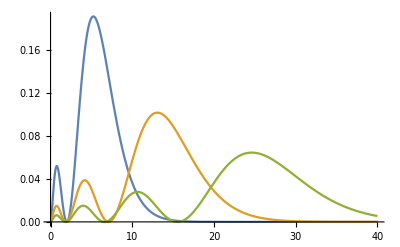

```mathematica
Plot[Evaluate[Table[Subscript[ℛ, n,0](r),{n,2,4}]],{r,0,40},PlotRange->All]
```

```mathematica
Manipulate[Plot[Evaluate[Subscript[ℛ, n,l](r)],{r,0,50},Filling->Axis,GridLines->Automatic],{{n,4},Range[2,5]},{{l,1},Range[0,n-1],ControlType->SetterBar}]
```

### Subsection. Density plots for pure basis states

We have so far plotted separately the angular and the radial distribution functions of various atomic orbitals.  However, these pictures are incomplete on their own and one needs to imaginatively assemble the angular and the radial plots in order to obtain a complete picture of the charge distribution in three-dimensional space.

For the pure basis state the probability distribution Ψ_(n,l,m)(r) is, as discussed earlier, axially symmetric, i.e.,

Ω_(n,l,m)(r,θ)=(|r R_(n,l)(r)Y_l^m(θ,ϕ)|)^2.

Mathematica's DensityPlot is then adequate for showing the detailed distribution of the two-variable function, where the lighter region indicates higher charge density:

```mathematica
Subscript[𝒫, n_,l_,m_](r_,θ_):=Subscript[ℛ, n,l](r) Subscript[Ω, l,m](θ)
```

Defining a set of rules to transform from spherical polar to Cartesian coordinates:

```mathematica
PolarToCartesian={r->√(x^2+y^2+z^2),θ->cos^-1(z/r),ϕ->tan^-1(x,y)};
```

the distribution in Cartesian coordinates is easily obtained:

```mathematica
Subscript[𝒞, n_,l_,m_](x_,y_,z_)=Subscript[𝒫, n,l,m](r,θ)//.PolarToCartesian;
```

Here are plots of the charge density in the x-z plane for n=2,3,4, l=1, m=0:

```mathematica
Manipulate[DensityPlot[Evaluate[Subscript[𝒞, n,1,0](x,0,z)],{x,-10,10},{z,-10,10},PlotPoints->30],{n,Range[2,4]}]
```

### Subsection. Three dimensional contour plots for mixed states

Finally, for a general coherent mixture of several magnetic states

ψ_(n,l)(r)=∑_m c_m ψ_(n,l,m)(r)=r R_(n,l)(r)∑_m c_m Y_l^m(θ,ϕ),

the total charge density distribution is a function of three variables (r,θ,ϕ):

```mathematica
Subscript[𝒫, n_,l_][c_][r_,θ_,ϕ_]:=Subscript[ℛ, n,l](r) Subscript[Ω, l][c][θ,ϕ]
```

Arbitrarily choosing C_1=1,  C_0=0,  C_-1=2/10, three dimensional contour surfaces of the total charge distribution in Cartesian coordinates,

```mathematica
FullSimplify[Subscript[𝒫, 2,1](({{1, 0}, {2/10, 0}}))(r,θ,ϕ)//.PolarToCartesian]
```

((4 x^2+9 y^2) ⅇ^(-√(x^2+y^2+z^2)) (x^2+y^2+z^2))/(400 π)

can be plotted using ContourPlot3D. Here are the surfaces for the contour levels 0.0003, 0.0015, and 0.003.

```mathematica
ContourPlot3D[%,{x,-15,0},{y,-15,15},{z,-12,12},Contours->{0.0003,0.0015,0.003},Mesh->None,BoxRatios->1,ContourStyle->Directive[Orange,Opacity[0.8],Specularity[White,30]]]
```

-Graphics3D-

## Section. MOLECULAR ORBITALS

As an example of multi-dimensional systems other than atomic orbitals, we consider the hydrogen molecule-ion, which consists of two nuclei and one electron. Its wavefunction can be represented by a linear combination of two atomic hydrogen wavefunctions:

ψ=∑_i c_i ϕ_i={1/(√(2 (1+s)))(ϕ_1(x-r_0,y,z)+ϕ_2(x+r_0,y,z)) | bondingorbitals,
1/(√(2 (1-s)))(ϕ_1(x-r_0,y,z)-ϕ_2(x+r_0,y,z)) | antibondingorbitals,

where 2 r_0 is the internuclear distance and S is a function of r_0. In Mathematica syntax, we have for the atomic wavefunction,

```mathematica
Subscript[ϕ, n_,l_,m_](x_,y_,z_)=r Subscript[R, n,l](r) Subscript[Y, l]^m(θ,ϕ)//.PolarToCartesian;
```

and for the molecular charge density of the bonding,

```mathematica
Subscript[ψ, B][({{n1_, l1_, m1_}, {n2_, l2_, m2_}})][x_,y_,z_]=(Subscript[ϕ, n1,l1,m1](x-2,y,z)+Subscript[ϕ, n2,l2,m2](x+2,y,z))^2;
```

Set::write: Tag List in (n1_/({_B) | l1_/({_B) | m1_/({_B)
n2_/({_B) | l2_/({_B) | m2_/({_B))(x_,y_,z_) is Protected.

and antibonding orbitals,

```mathematica
Subscript[ψ, A][({{n1_, l1_, m1_}, {n2_, l2_, m2_}})][x_,y_,z_]=(Subscript[ϕ, n1,l1,m1](x-2,y,z)-Subscript[ϕ, n2,l2,m2](x+2,y,z))^2;
```

Set::write: Tag List in (n1_/({_A) | l1_/({_A) | m1_/({_A)
n2_/({_A) | l2_/({_A) | m2_/({_A))(x_,y_,z_) is Protected.

If the hydrogen molecular-ion is in the state n_1=1, l_1=0, m_1=0, n_2=1, l_2=0, m_2=0, both bonding and antibonding orbitals have cylindrical symmetry along the internuclear x-z plane. The DensityPlot command is used to depict the projection of the charge distribution in this plane.

```mathematica
DensityPlot[Evaluate[Subscript[ψ, B][({{1, 0, 0}, {1, 0, 0}})][x,0,z]],{x,-5,5},{z,-5,5},PlotPoints->80]
```

```mathematica
DensityPlot[Evaluate[Subscript[ψ, A][({{1, 0, 0}, {1, 0, 0}})][x,0,z]],{x,-5,5},{z,-5,5},PlotPoints->80]
```

To see these orbitals in three dimensions, we also plot their contour surface at an arbitrary level of 0.005:

```mathematica
ContourPlot3D[Evaluate[Subscript[ψ, B][({{1, 0, 0}, {1, 0, 0}})][x,y,z]==0.005],{x,-6,6},{y,-5,5},{z,-5,5},Mesh->None,BoxRatios->1,ContourStyle->Directive[Orange,Opacity[0.8],Specularity[White,30]]]
```

```mathematica
ContourPlot3D[Evaluate[Subscript[ψ, A][({{1, 0, 0}, {1, 0, 0}})][x,y,z]==0.005],{x,-6,6},{y,-5,5},{z,-5,5},Mesh->None,BoxRatios->1,ContourStyle->Directive[Orange,Opacity[0.8],Specularity[White,30]]]
```

## Section. EXAMPLES OF SYMBOLIC ANALYSIS

### Subsection. Clebsch-Gordan coefficients

Clebsch-Gordan, 3-j, 6-j and 9-j coefficients (CGC) arise when coupling together angular momentum states or, equivalently, when linearizing products of or computing integrals over spherical harmonics.  It is important to note that Mathematica can compute both numerical and symbolic CGC.

Advantages of  symbolic computation of CGC include evaluating whole classes of related coefficients in one operation, and easy conversion to fortran or C (using FortranForm or CForm), if rapid computation is required.

### Subsection. Products and integrals of spherical harmonics

Products of spherical harmonics arise when computing the electron density of atomic states.  Using the CGC, it is straightforward to linearize these products via

Y_l_1^m_1(θ,ϕ) Y_l_2^m_2(θ,ϕ)=∑_(l_3=|l_1-l_2|)^(l_1+l_2) ∑_(m=-l_3)^l_3 √(((2 l_1+1)(2 l_2+1)(2 l_3+1))/(4π))(l_1 | l_2 | l_3
0 | 0 | 0)(l_1 | l_2 | l_3
m_1 | m_2 | m_3) (Y_l_3^m_3(θ,ϕ))^* .

This result can be used to evaluate the general integral of a triple product of spherical harmonics,

∫_0^(2π) ∫_0^π Y_l_1^m_1(θ,ϕ) Y_l_2^m_2(θ,ϕ) Y_l_3^m_3(θ,ϕ) sin(θ)ⅆθⅆϕ=√(((2 l_1+1)(2 l_2+1)(2 l_3+1))/(4π))(l_1 | l_2 | l_3
0 | 0 | 0)(l_1 | l_2 | l_3
m_1 | m_2 | m_3).

In Mathematica this formula can be entered as follows:

```mathematica
TripleProduct[{l1_,m1_},{l2_,m2_},{l3_,m3_}]:=√(((2l1+1)(2l2+1)(2l3+1))/(4π)) ( {{l1, l2, l3}, {m1, m2, m3}} )  ( {{l1, l2, l3}, {0, 0, 0}} )
```

```mathematica
Notation[⟨{{j1_, j2_, j3_}, {m1_, m2_, m3_}} ⟩ ⟺ TripleProduct[{j1_, m1_}, {j2_, m2_}, {j3_, m3_}]]
```

This expression is used in the following example of the linear Stark effect.

### Subsection. Stark effect

The linear Stark effect requires the computation of the matrix elements ⟨n l m|r cos(θ)|n l±1m⟩. Noting that cos(θ) is equivalent to 2 √(π/3) Y_1^0(θ,ϕ),

```mathematica
2 √(π/3) Subscript[Y, 1]^0(θ,ϕ)==cos(θ)
```

True

and that

(Y_l^m(θ,ϕ))^*=Y_l^m(θ,-ϕ)=(-1)^m Y_l^-m(θ,ϕ),

the required non-vanishing angular integrals, i.e., ⟨l m|cos(θ)|l±1m⟩, are easily evaluated.

```mathematica
FullSimplify[2 √(π/3) (-1)^m ⟨{{l, 1, l+1}, {-m, 0, m}} ⟩,l≥m≥0∧{l,m}∈ℤ]
```

√(((l-m+1) (l+m+1))/(4 l (l+2)+3))

```mathematica
Factor[%^2]
```

((l-m+1) (l+m+1))/((2 l+1) (2 l+3))

## Section. CONCLUDING REMARKS

This article has demonstrated the capabilities of Mathematica for analyzing and visualizing atomic systems. The interplay between symbolic and graphical methods yields a tool that is more powerful than the sum of its parts and one that can be superior to special purpose visualization tools because of its flexibility.

Even for readers that have never used a computer algebra system, an examination of some of the code fragments presented above — say those implementing the radial wavefunctions for hydrogenic atoms or the triple integral of spherical harmonics — illustrates that implementing some quite complicated formulae in Mathematica is straightforward and transparent and, hence, less likely to contain or conceal an error. One of the goals of object oriented programming is to implement high-level structures.  All of the computations in this article could, of course, be done in fortran or C (or C++).  However, in general, the physicist or chemist does not want to write packages for computing orthogonal polynomials, spherical harmonics, Clebsch-Gordan coefficients or basic graphical tools. Of course, there exists libraries of public domain and commercial software which, when linked together, can provide equivalent capabilities. But, since all these capabilities, along with general symbolic manipulation, are built-in to Mathematica it can be seen to be an ideal tool for a wide range of analysis of atomic and molecular systems.

## REREFENCES

1. R.S. Berry, J. Chem. Ed. 43, 283 (1966)

2. S. Wolfram, Mathematica: A System for Doing Mathematics by Computer (Addison-Wesley, Reading, 1991)

3. A.R. Edmonds, Angular Momentum in Quantum Mechanics (Princeton, New Jersey, 1974)

4. B.H. Bransden and C.J. Joachain, Physics of Atoms and Molecules (Longman, UK, 1989)

5. K. Blum, Density Matrix Theory and Applications (Plenum: New York, 1981)

6. M. Abramowitz and I.A. Stegun, Handbook of Mathematical Functions (Dover, New York, 1972)

7. J.F. Shriner and W.J. Thompson, Computers in Physics, 7, 144 (1993)